```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[par_]:=Block[{},
Write["in.txt",#]&/@par;
Close["in.txt"];
Run["./air_v3 < in.txt"];
d = Import["out_data.txt","Table"];
name="";
Do[name=name<>ToString[par[[i]]]<>"_",{i,Length[par]}];
Run["mv out_data.txt "<>name<>".txt"];

l=ListPlot[{d},Axes->False, AspectRatio->{1,1}, PlotRange->All];
l
]
```

```mathematica
gMax[alp_,bet_]:=ArcCos[1.-2*Sin[(alp+bet)/2]^2]
```

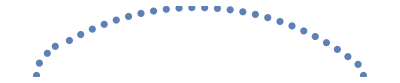
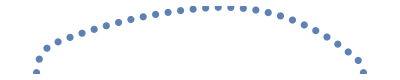

```mathematica
alp1 = Pi/8.;bet1=Pi/5.;
alp2 = Pi/10.;bet2=-Pi/8.;
gam2 = 0.0418879;
Reap[Do[Sow[
f[{alp1,bet1,gam1,alp2,bet2,gam2}]],{gam1,0.001,gMax[alp1,bet1],gMax[alp1,bet1]/2}]][[2,1]]
```